#### Born Oppenheimer Approximation

a) Making the BO approximation, write the purely electronic Hamiltonian and, by completing the square,
write its energy levels, E_(el,n)(X).

```mathematica
Elec[n_]:=(n+1/2)Sqrt[2]+(3 X^2)/4
```

b) Write the nuclear equation for the proton in the field of the electronic energy plus any other
parts of the potential, to get an expression for the total energy of the system, E_(ν,n), where ν is the
quantum number for proton vibrations.

```mathematica
Etot[ν_,n_,m_]:=(ν+1/2 )Sqrt[3/(2m)]+(n+1/2)Sqrt[2]
```

c) Assuming m=25, plot the lowest 12 levels, labeling them with their electronic and nuclear quantum
numbers.

```mathematica
ntotstate[ν_,n_,m_]:=Table[Etot[i,n,m],{i,0,12}]
```

```mathematica
ntotstate[12,0,25]//N
```

{0.829581,1.07453,1.31948,1.56443,1.80938,2.05433,2.29928,2.54422,2.78917,3.03412,3.27907,3.52402,3.76897}

```mathematica
ntotstate[12,1,25]//N
```

{2.24379,2.48874,2.73369,2.97864,3.22359,3.46854,3.71349,3.95844,4.20339,4.44834,4.69328,4.93823,5.18318}

```mathematica
ntotstate[12,2,25]//N
```

{3.65801,3.90296,4.14791,4.39286,4.6378,4.88275,5.1277,5.37265,5.6176,5.86255,6.1075,6.35245,6.5974}

d) The exact solution to this problem is given by the sum of two harmonic oscillators. Show that, if m>>1,
this agrees with your BO solutions above.

e) Plot the exact energy levels and compare with the BO solution. Plot the errors of the BO energies as a
function of energy. How accurate is BO for the lowest energy state? Does the accuracy depend on where
you are in the spectrum?

```mathematica
exactsumHO[ν_,n_,m_]:=(1+1/m+Sqrt[1-1/m+1/m^2])^(1/2)(n+1/2)+(1+1/m-Sqrt[1-1/m+1/m^2])^(1/2)(ν+1/2)
nexactstate[ν_,n_,m_]:=Table[exactsumHO[i,n,m],{i,0,12}]
```

```mathematica
nexactstate[12,0,25]//N
```

{0.832589,1.07629,1.31998,1.56368,1.80738,2.05107,2.29477,2.53846,2.78216,3.02586,3.26955,3.51325,3.75695}

```mathematica
nexactstate[12,1,25]//N
```

{2.25407,2.49777,2.74146,2.98516,3.22886,3.47255,3.71625,3.95995,4.20364,4.44734,4.69104,4.93473,5.17843}

```mathematica
error[n_,ν_,m_]:=Abs[Etot[ν,n,m]-exactsumHO[ν,n,m]]/exactsumHO[ν,n,m]*100
taberr[n_,ν_,m_]:=Table[{i,error[n,i,m]//N},{i,0,ν}]
```

```mathematica
taberr[0,12,27]
```

{{0,0.33841},{1,0.158807},{2,0.0441768},{3,0.0353371},{4,0.0937277},{5,0.138425},{6,0.173741},{7,0.202348},{8,0.225993},{9,0.245863},{10,0.262795},{11,0.277397},{12,0.290118}}

```mathematica
taberr[1,12,27]
```

{{0,0.42326},{1,0.33841},{2,0.268208},{3,0.209161},{4,0.158807},{5,0.115358},{6,0.0774837},{7,0.0441768},{8,0.0146578},{9,0.0116846},{10,0.0353371},{11,0.0566916},{12,0.0760675}}

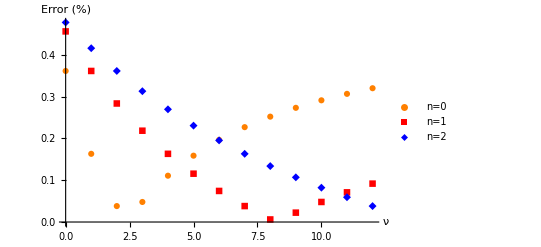

```mathematica
p1=ListPlot[{taberr[0,12,25],taberr[1,12,25],taberr[2,12,25]},AxesLabel->{"ν","Error (%)"},LabelStyle->Medium,PlotMarkers->Automatic,PlotStyle->{Orange,Red,Blue},PlotLegends->Placed[{"n=0","n=1","n=2"},{0.9,0.85}]]
```

```mathematica
Export["error_bo_m25.eps",p1]
```

f) Repeat your calculation for m = 27, and comment on the errors in the BO states near the first electronic
excitation. In particular, comment on (near)-degeneracies.

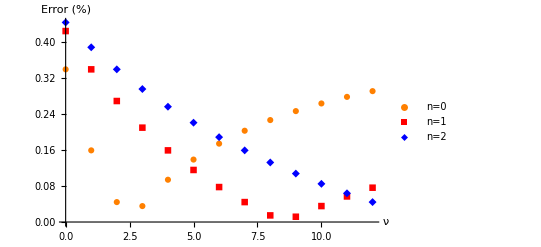

```mathematica
p2=ListPlot[{taberr[0,12,27],taberr[1,12,27],taberr[2,12,27]},AxesLabel->{"ν","Error (%)"},LabelStyle->Medium,PlotMarkers->Automatic,PlotStyle->{Orange,Red,Blue},PlotLegends->Placed[{"n=0","n=1","n=2"},{0.9,0.85}]]
```

```mathematica
Export["error_bo_m27.eps",p2]
```

error_bo_m27.eps

#### General Problems about Diatomics from

1. Find ρ and B in equation 7.43

```mathematica
mayer[R_]:=B*Exp[-R/ρ]
polar[α1_,α2_,R_]:=-(α1+α2)/(2 R^4)
```

```mathematica
0.29397970028+0.338461053
```

0.632441

```mathematica
{7.9996+9.21,6.513+7.14,5.616+6.1,5.993+6.63,4.458+4.72,4.835+5.17,4.692+4.96}
```

{17.2096,13.653,11.716,12.623,9.178,10.005,9.652}

```mathematica
FindFit[{{1.564,7.9996+9.21},{2.021,6.513+7.14},{2.361,5.616+6.1},{2.171,5.993+6.63},{3.048,4.458+4.72},{2.7869,4.835+5.17},{2.906,4.692+4.96}},B*Exp[-R/ρ],{B,ρ},R]
```

{B→33.056,ρ→2.32365}

```mathematica
33.056*Exp[-1.564/2.32365]
```

16.863

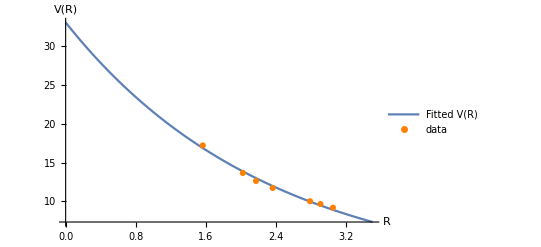

```mathematica
Show[Plot[33.056*Exp[-R/2.32365],{R,0,3.5},AxesLabel->{"R","V(R)"},TicksStyle->Medium,AxesStyle->Medium,PlotLegends->{"Fitted V(R)"}],ListPlot[{{1.564,7.9996+9.21},{2.021,6.513+7.14},{2.361,5.616+6.1},{2.171,5.993+6.63},{3.048,4.458+4.72},{2.7869,4.835+5.17},{2.906,4.692+4.96}},PlotStyle->Orange,PlotMarkers->Automatic,PlotLegends->{"data"}]]
```

```mathematica
{919,559.7,323.3,214.5}
```

{919,559.7,323.3,214.5}

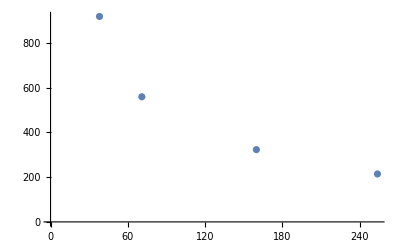

```mathematica
ListPlot[{{18.998*2,919},{2*35.45,559.7},{2*79.904,323.3},{2*126.9,214.5}}]
```

```mathematica
FindFit[{{2*79.904,323.3},{2*126.9,214.5}},b+a x,{a,b},x]
```

{a→-1.15755,b→508.285}

```mathematica
508.285-1.15755*420
```

22.114

```mathematica
FindFit[{{2*79.904,2.281},{2*126.9,2.667}},b+a x,{a,b},x]
```

{a→0.00410673,b→1.62471}

```mathematica
1.62471+0.0041063*420
```

3.34936

```mathematica
FindFit[{{2*79.904,1.971},{2*126.9,1.544}},b+a x,{a,b},x]
```

{a→-0.00454294,b→2.697}

```mathematica
2.697-0.00454294*420
```

0.788965

```mathematica
FindFit[{{2*85.468,57.3},{2*132.91,42}},b+a x,{a,b},x]
```

{a→-0.16125,b→84.8633}

```mathematica
84.633-0.16125*446
```

12.7155

```mathematica
FindFit[{{2*85.468,4.2},{2*132.91,4.58}},b+a x,{a,b},x]
```

{a→0.00400489,b→3.51542}

```mathematica
3.51542+0.00400489*446
```

5.3016

```mathematica
FindFit[{{2*85.468,0.47},{2*132.91,0.45}},b+a x,{a,b},x]
```

{a→-0.000210784,b→0.506031}

```mathematica
0.506031-0.000210784*446
```

0.412021

```mathematica
FindFit[{{1.008+79.904,1.414},{1.008+126.9,1.609}},b+a x,{a,b},x]
```

{a→0.00414929,b→1.07827}

```mathematica
1.07827+0.00414929*211
```

1.95377

```mathematica
FindFit[{{1.008+79.904,3.755},{1.008+126.9,3.053}},b+a x,{a,b},x]
```

{a→-0.0149374,b→4.96362}

```mathematica
4.96362-0.0149374*211
```

1.81183

```mathematica
-D[(x-X)^2+x X,X]//Simplify
```

x-2 X

```mathematica
4400.39*100*6.262*10^-34
```

2.75552×10^-28

```mathematica
energy[ν_,x_,y_,h_]:=h ν*(1/2-x/4+y/8)
```

```mathematica
energy[4400.39*3.00*10^10,120.815/4400.39,0.7242/4400.39,6.626*10^-34*100^2]/100^2
```

4.31369×10^-20

```mathematica
%*2.293712658*10^17
```

0.00989436

```mathematica
6.626*10^-34*4400.39*100*2.294*10^17/2
```

3.34431×10^-11

```mathematica
D[b(Exp[-2 a R]-2Exp[-a R]),R]
```

b (-2 a ⅇ^(-2 a R)+2 a ⅇ^(-a R))